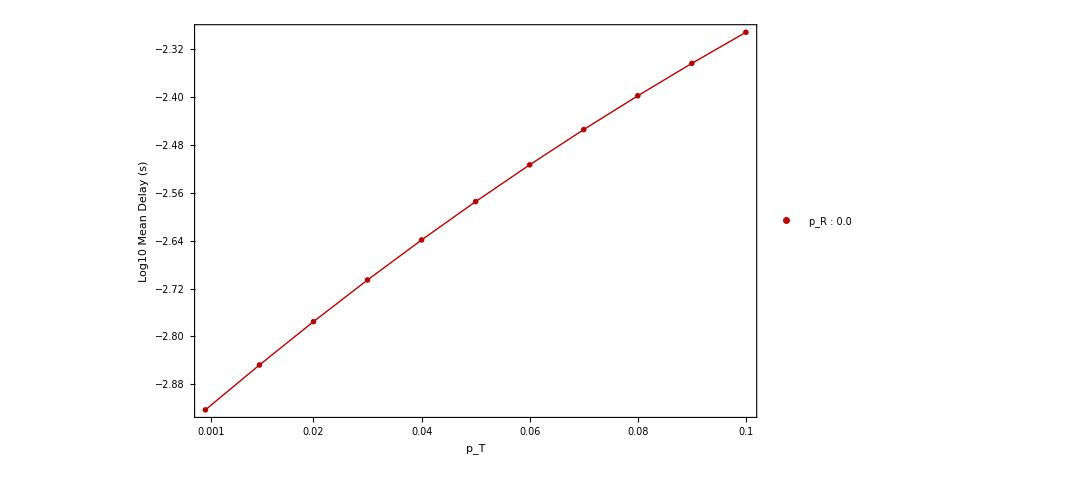

28.3465

```mathematica
(* Maxumun number of retransmissions, assumed to be infinity but this is enough *)
stepsMax=10;

(* Range of packet loss values *)
Pinit=0.01;
Pend  =0.11;
Pstep=0.01;

(* Number of stations *)
Ninit=15;
Nend=15;
Nstep=15;

(* Loss probability of retransmission packet *)
(*
Unprotect[Power];
Power[0,0]=1;
Protect[Power];
*)
pR=0.1;

(* Probability of channel access for data and retr. req. packet, F - forward data packet, R - retr. packet *)
rT=0.2;
rQ=0.2;

(* Duration of a time slot *)
slt=0.00001;

(*Time to transmit the data packet (Tt) and retrnamission request (Tq), respectively, Tq<<Tt as data packets is usually longer *)
Tt= 0.001;
Tq= 0.0001;

(* Time to wait to get the packet of interest as a result of the sent request *)

Tconst = 0.0012;

(* Arrays to store PDF, CDF, Variance, Mean and quantile of the number of steps till absorbtion *)
singlePMFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleCDFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];

singleVarArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];
singleMeanArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Arrays to store PDF, Mean and quantile of delay till absorbtion *)
singlePMFDelay=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleMeanDelay1=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Definiting Binomial distribution *)
BD[n_,p_,i_]:=Binomial[n,i]*(p^i)*(1-p)^n/(1-p)^i;

i=1;
j=1;

Do[
Do[

(* PARAMETERIZATION *)

(* Matrix Q of the absorbing Markov chain chain: jumping between transient states *)
Q=Table[0*k*n,{n,1,currN},{k,1,currN}];


For[n=1,n<currN+1,n++,
For[k=1,k<currN+1,k++,
If[k==n,If[n==currN,Part[Q,n,k]=Power[currP,n],Part[Q,n,k]=Power[pR,currN-n]+(1-Power[pR,currN-n])*Power[currP,n]]];
If[k<n,If[n==currN,Part[Q,n,k]=BD[n,currP,k],Part[Q,n,k]=(1-Power[pR,currN-n])*BD[n,currP,k]]];
];
];

(* Print["Matrix Q: ",TableForm[Q]]; *)

(* Defining vector t of the chain: absorbtion from every state *)
t=Table[0*n,{n,1,currN}];

For[n=1,n<currN+1,n++,
If[n≠currN,Part[t,n]=(1-Power[pR,currN-n])*(Power[1-currP,n]),Part[t,n]=Power[1-currP,currN]];
];

(* Print["vector t: ",TableForm[t]]; *)

(* Defining initial state probability vector: we always start with N stations not having a packet *)
v=Table[0*n,{n,1,currN}];
Part[v,currN]=1;

(* Print["vector v: ",TableForm[v]]; *)

(* COMPUTING METRICS FOR A SINGLE PACKET *)

(* Supplementary entities *)
e=Table[0*n+1,{n,1,currN}];

(* Print["vector e: ",TableForm[e]]; *)

(* PMF of the number of steps till absrobtion: gives PMF of the delay *)
stepsPMF=Table[v.If[n≠0,MatrixPower[Q,n],IdentityMatrix[currN]].t,{n,0,stepsMax}];

(* Print["stepsPMF: ",TableForm[stepsPMF]]; *)

(* Testing whether PMF sums up to one, if not increase the stepsMax*)
If[Sum[Part[stepsPMF,n],{n,0,stepsMax}]<0.99||Sum[Part[stepsPMF,n],{n,0,stepsMax}]>1.01,Print["PMF does not sum up to 1!"]];

(* Print["PMF sum to 1? ",TableForm[Sum[Part[stepsPMF,n],{n,1,stepsMax}]]]; *)

(* CDF of the number of steps till absrobtion: gives CDF of the delay *)

stepsCDF=Table[Sum[Part[stepsPMF,n],{n,1,k}],{k,1,stepsMax}];
(* Mean number of steps before absorbtion: gives mean delay *)
stepsMean=Sum[Part[stepsPMF,n]*n,{n,1,stepsMax}];

(* Print["steps Mean: ",TableForm[stepsMean]]; *)

(* Variance of the number of steps *)
stepsVar=Sum[Part[stepsPMF,n]*Power[(n-stepsMean),2],{n,1,stepsMax}];

(* Print["steps Variance: ",TableForm[stepsVar]]; *)

(* We can also get probabilities that k, k=1,2,..,N stations not having a packet after k step this is a vector: v*Q^{k} *)

(* Computing the Fundamental matrix *)
Z=Inverse[IdentityMatrix[currN]-Q];

(* Computing hi as the probability of being in the arbitrary state i after original transmission of the packet *)
(*h =Table [ PDF[BinomialDistribution[currN,pR],n],{n,0,currN}];*)

(* Probability of visiting a transient state j when starting in transient state i *)
Zdq=DiagonalMatrix[Diagonal[Z]];
visitPrMatrix=(Z-IdentityMatrix[currN]).Inverse[Zdq];

 (* Print["Matrix Z: ",TableForm[Z]]; *)

(* Print["Visits V: ",TableForm[visitPrMatrix]]; *)

(* CONDITIONAL DELAY IN A CERTAIN STATE *)
(* Array for conditional delays for failure and overall *)
condDelayFail=Table[0,{k,1,currN}];
condDelayAll=Table[0,{k,1,currN}];

(* Computing conditional delays for states starting from 1 to N-1: in case of failure *)
For [n=1,n<currN+1,n++,
  Part[condDelayFail,n] = Tconst;
];


(* Computing the mean delay in the arbitrary state i: for non-zero request packet loss probabilities *)

For [n=1,n<currN+1,n++,
Part[condDelayAll,n]= 1/Part[Q,n,n]*Part[condDelayFail,n]+((1/rQ)*slt) + Tq  +((1/rT)*slt) + Tt;
];

(*
For [i=1,i<currN+1,i++,
 Print["Conditional delay all ",i,": ",TableForm[Part[condDelayAll,i]]];
];
*)

(* Computing the mean delay till absorption *)

overallDelay1 =Tt + Sum[BD[currN,currP,n]*Part[condDelayAll,k]*Part[visitPrMatrix,n,k],{n,1,currN},{k,1,n}];

(*  Print["Overall Delay: ",TableForm[overallDelay]]; *)

(* Storing PMF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singlePMFArray,i,j,2,n]=Part[stepsPMF,n];
Part[singlePMFArray,i,j,1,n]=n;
];

(* Print["PMF of steps till absorption: ",TableForm[singlePMFArray]]; *)

(* Storing CDF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singleCDFArray,i,j,2,n]=Part[stepsCDF,n];
Part[singleCDFArray,i,j,1,n]=n;
];

(* Print["CDF of steps till absorption: ",TableForm[singleCDFArray]]; *)

(* Storing Variance of the number of steps to global matrices*)
Part[singleVarArray,i,j]=stepsVar;
(* Print["Variance of steps till absorption: ",TableForm[singleVarArray]]; *)


(* Storing Mean of the number of steps to global matrices*)
Part[singleMeanArray,i,j]=stepsMean;
(* Print["Mean of the number of steps till absorption: ",TableForm[singleMeanArray]]; *)


(* Storing Mean of the delay to global matrices *)
Part[singleMeanDelay1,i,j]=overallDelay1;
 (*  Print["Mean of the delay till absorption: ",TableForm[singleMeanDelay]]; *)

(* PMF and CDF of delay not for this version *)


(* ENDING THE CYCLES *)
i++;,
{currP,Pinit,Pend,Pstep}];

i=1;
j++;,


{currN,Ninit,Nend,Nstep}];


markers3 = { {-Graphics-, 0.04}};

splot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay1,1,1],Part[singleMeanDelay1,2,1],Part[singleMeanDelay1,3,1],Part[singleMeanDelay1,4,1],Part[singleMeanDelay1,5,1],Part[singleMeanDelay1,6,1],Part[singleMeanDelay1,7,1],Part[singleMeanDelay1,8,1],Part[singleMeanDelay1,9,1],Part[singleMeanDelay1,10,1],Part[singleMeanDelay1,11,1]}],DataRange->{0.0,0.1},Filling->None,Frame->True ,FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Log10 Mean Delay (s)",Black,25]},PlotMarkers->markers3,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[85,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{Subscript[p,R]," : 0.0"#}]&/@Range[4],LegendMarkers->markers3 ,LegendMarkerSize->14,LabelStyle->{GrayLevel[0.1],19}],{0.14,0.9}]],BaseStyle->{FontSize->19}]

cm=72/2.54 (*centimetres*)
```

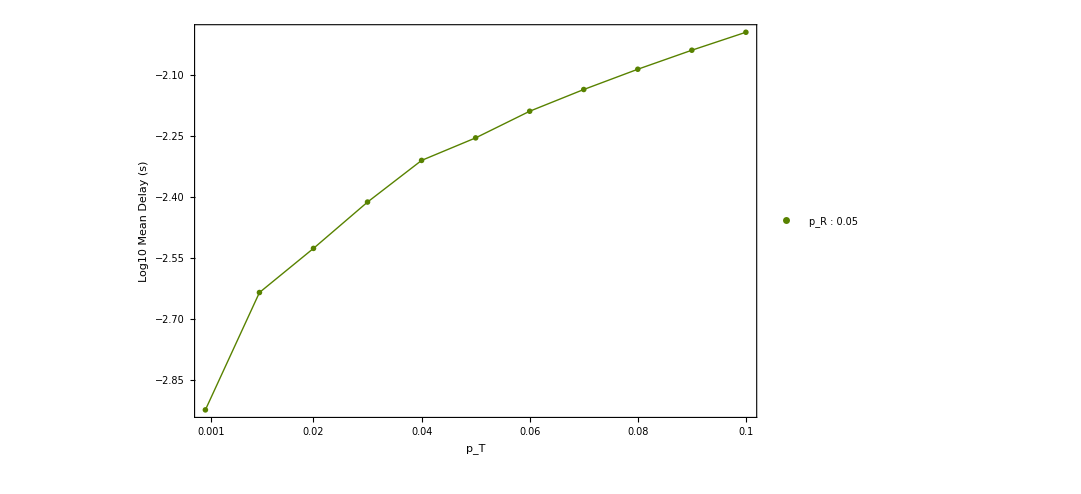

ColorData::notent: RGBColor[0, 0, 1] is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: Directive[AbsoluteThickness[1], RGBColor[0, 0, 1]] is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

ColorData::notent: {AbsoluteThickness[1], RGBColor[0, 0, 1]} is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

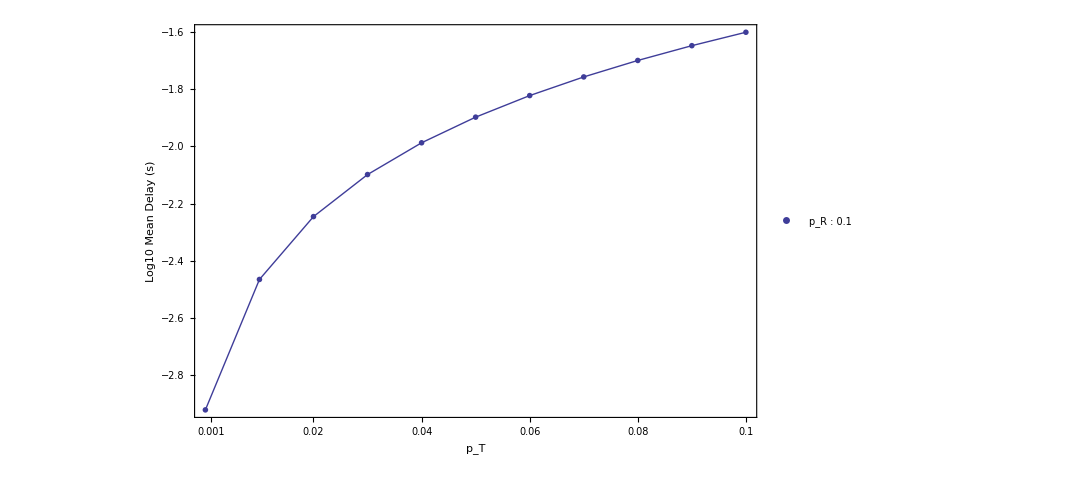

28.3465

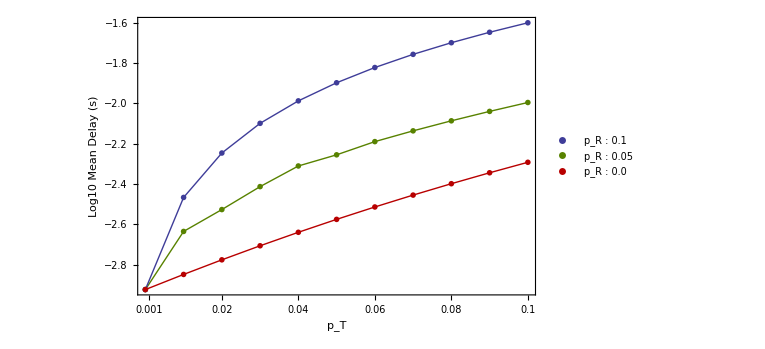

MeanDelay-ret-req-log.eps

```mathematica
(* second round for second pR *)

(* Maxumun number of retransmissions, assumed to be infinity but this is enough *)
stepsMax=10;

(* Range of packet loss values *)
Pinit=0.01;
Pend  =0.11;
Pstep=0.01;

(* Number of stations *)
Ninit=15;
Nend=15;
Nstep=15;

(* Loss probability of retransmission packet *)
(*
Unprotect[Power];
Power[0,0]=1;
Protect[Power];
*)
pR=0.05;

(* Probability of channel access for data and retr. req. packet, F - forward data packet, R - retr. packet *)
rT=0.2;
rQ=0.2;

(* Duration of a time slot *)
slt=0.00001;

(*Time to transmit the data packet (Tt) and retrnamission request (Tq), respectively, Tq<<Tt as data packets is usually longer *)
Tt= 0.001;
Tq= 0.0001;

(* Time to wait to get the packet of interest as a result of the sent request *)

Tconst = 0.0012;

(* Arrays to store PDF, CDF, Variance, Mean and quantile of the number of steps till absorbtion *)
singlePMFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleCDFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];

singleVarArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];
singleMeanArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Arrays to store PDF, Mean and quantile of delay till absorbtion *)
singlePMFDelay=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleMeanDelay2=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Definiting Binomial distribution *)
BD[n_,p_,i_]:=Binomial[n,i]*(p^i)*(1-p)^n/(1-p)^i;

i=1;
j=1;

Do[
Do[

(* PARAMETERIZATION *)

(* Matrix Q of the absorbing Markov chain chain: jumping between transient states *)
Q=Table[0*k*n,{n,1,currN},{k,1,currN}];


For[n=1,n<currN+1,n++,
For[k=1,k<currN+1,k++,
If[k==n,If[n==currN,Part[Q,n,k]=Power[currP,n],Part[Q,n,k]=Power[pR,currN-n]+(1-Power[pR,currN-n])*Power[currP,n]]];
If[k<n,If[n==currN,Part[Q,n,k]=BD[n,currP,k],Part[Q,n,k]=(1-Power[pR,currN-n])*BD[n,currP,k]]];
];
];

(* Print["Matrix Q: ",TableForm[Q]]; *)

(* Defining vector t of the chain: absorbtion from every state *)
t=Table[0*n,{n,1,currN}];

For[n=1,n<currN+1,n++,
If[n≠currN,Part[t,n]=(1-Power[pR,currN-n])*(Power[1-currP,n]),Part[t,n]=Power[1-currP,currN]];
];

(* Print["vector t: ",TableForm[t]]; *)

(* Defining initial state probability vector: we always start with N stations not having a packet *)
v=Table[0*n,{n,1,currN}];
Part[v,currN]=1;

(* Print["vector v: ",TableForm[v]]; *)

(* COMPUTING METRICS FOR A SINGLE PACKET *)

(* Supplementary entities *)
e=Table[0*n+1,{n,1,currN}];

(* Print["vector e: ",TableForm[e]]; *)

(* PMF of the number of steps till absrobtion: gives PMF of the delay *)
stepsPMF=Table[v.If[n≠0,MatrixPower[Q,n],IdentityMatrix[currN]].t,{n,0,stepsMax}];

(* Print["stepsPMF: ",TableForm[stepsPMF]]; *)

(* Testing whether PMF sums up to one, if not increase the stepsMax*)
If[Sum[Part[stepsPMF,n],{n,0,stepsMax}]<0.99||Sum[Part[stepsPMF,n],{n,0,stepsMax}]>1.01,Print["PMF does not sum up to 1!"]];

(* Print["PMF sum to 1? ",TableForm[Sum[Part[stepsPMF,n],{n,1,stepsMax}]]]; *)

(* CDF of the number of steps till absrobtion: gives CDF of the delay *)

stepsCDF=Table[Sum[Part[stepsPMF,n],{n,1,k}],{k,1,stepsMax}];
(* Mean number of steps before absorbtion: gives mean delay *)
stepsMean=Sum[Part[stepsPMF,n]*n,{n,1,stepsMax}];

(* Print["steps Mean: ",TableForm[stepsMean]]; *)

(* Variance of the number of steps *)
stepsVar=Sum[Part[stepsPMF,n]*Power[(n-stepsMean),2],{n,1,stepsMax}];

(* Print["steps Variance: ",TableForm[stepsVar]]; *)

(* We can also get probabilities that k, k=1,2,..,N stations not having a packet after k step this is a vector: v*Q^{k} *)

(* Computing the Fundamental matrix *)
Z=Inverse[IdentityMatrix[currN]-Q];

(* Computing hi as the probability of being in the arbitrary state i after original transmission of the packet *)
(*h =Table [ PDF[BinomialDistribution[currN,pR],n],{n,0,currN}];*)

(* Probability of visiting a transient state j when starting in transient state i *)
Zdq=DiagonalMatrix[Diagonal[Z]];
visitPrMatrix=(Z-IdentityMatrix[currN]).Inverse[Zdq];

 (* Print["Matrix Z: ",TableForm[Z]]; *)

(* Print["Visits V: ",TableForm[visitPrMatrix]]; *)

(* CONDITIONAL DELAY IN A CERTAIN STATE *)
(* Array for conditional delays for failure and overall *)
condDelayFail=Table[0,{k,1,currN}];
condDelayAll=Table[0,{k,1,currN}];

(* Computing conditional delays for states starting from 1 to N-1: in case of failure *)
For [n=1,n<currN+1,n++,
  Part[condDelayFail,n] = Tconst;
];


(* Computing the mean delay in the arbitrary state i: for non-zero request packet loss probabilities *)

For [n=1,n<currN+1,n++,
Part[condDelayAll,n]= 1/Part[Q,n,n]*Part[condDelayFail,n]+((1/rQ)*slt) + Tq  +((1/rT)*slt) + Tt;
];

(*
For [i=1,i<currN+1,i++,
 Print["Conditional delay all ",i,": ",TableForm[Part[condDelayAll,i]]];
];
*)

(* Computing the mean delay till absorption *)

overallDelay2 =Tt + Sum[BD[currN,currP,n]*Part[condDelayAll,k]*Part[visitPrMatrix,n,k],{n,1,currN},{k,1,n}];

(*  Print["Overall Delay: ",TableForm[overallDelay]]; *)

(* Storing PMF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singlePMFArray,i,j,2,n]=Part[stepsPMF,n];
Part[singlePMFArray,i,j,1,n]=n;
];

(* Print["PMF of steps till absorption: ",TableForm[singlePMFArray]]; *)

(* Storing CDF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singleCDFArray,i,j,2,n]=Part[stepsCDF,n];
Part[singleCDFArray,i,j,1,n]=n;
];

(* Print["CDF of steps till absorption: ",TableForm[singleCDFArray]]; *)

(* Storing Variance of the number of steps to global matrices*)
Part[singleVarArray,i,j]=stepsVar;
(* Print["Variance of steps till absorption: ",TableForm[singleVarArray]]; *)


(* Storing Mean of the number of steps to global matrices*)
Part[singleMeanArray,i,j]=stepsMean;
(* Print["Mean of the number of steps till absorption: ",TableForm[singleMeanArray]]; *)


(* Storing Mean of the delay to global matrices *)
Part[singleMeanDelay2,i,j]=overallDelay2;
 (*  Print["Mean of the delay till absorption: ",TableForm[singleMeanDelay]]; *)

(* PMF and CDF of delay not for this version *)


(* ENDING THE CYCLES *)
i++;,
{currP,Pinit,Pend,Pstep}];

i=1;
j++;,


{currN,Ninit,Nend,Nstep}];

markers2 = { {-Graphics-, 0.04}};

cplot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay2,1,1],0.0009+Part[singleMeanDelay2,2,1],0.0013+Part[singleMeanDelay2,3,1],0.0019+Part[singleMeanDelay2,4,1],0.0026+Part[singleMeanDelay2,5,1],0.0029+Part[singleMeanDelay2,6,1],0.0034+Part[singleMeanDelay2,7,1],0.0038+Part[singleMeanDelay2,8,1],0.0042+Part[singleMeanDelay2,9,1],0.0046+Part[singleMeanDelay2,10,1],0.005+Part[singleMeanDelay2,11,1]}],DataRange->{0.0,0.1},Filling->None,Frame->True ,FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Log10 Mean Delay (s)",Black,25]},PlotMarkers->markers2,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[75,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{Subscript[p,R]," : 0.05"#}]&/@Range[4],LegendMarkers->markers2 ,LegendMarkerSize->14,LabelStyle->{GrayLevel[0.1],19}],{0.15,0.8}]],BaseStyle->{FontSize->19}]

(*
cplot = ListPlot[Evaluate[{Part[singleMeanDelay2,10,1],Part[singleMeanDelay2,20,1],Part[singleMeanDelay2,30,1],Part[singleMeanDelay2,40,1],Part[singleMeanDelay2,50,1]},DataRange->{0.0,0.5},Filling->None,Frame->True ,FrameTicks->{{Automatic,None},{{0.0001,0.1,0.2,0.3,0.4,0.5},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Log10 Mean Delay (s)",Black,25]},PlotMarkers->markers2,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[75,"ColorList"]),ImageSize->1000,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,PlotLegends->Placed[PointLegend[Row[{Subscript[p,R]," : 0.05"#}]&/@Range[4],LegendMarkers->markers2 ,LegendMarkerSize->18,LabelStyle->{GrayLevel[0.1],20}],{0.15,0.8}]],BaseStyle->{FontSize->30}]
*)


(* FrameTicks->{{Automatic,None},{{0.0001,0.1,0.2,0.3,0.4,0.5},None}} *)


(*
 DO:
 - no collision-related losses;
  - losses of retransmission requests due to wireless medium;
  - losses of informational packets due to wireless medium
GET:
- PMF on the number of retr. attempts to deliver a packet and message to all the stations;
  - PMF and CDF of the delay;
  - mean delay till all get the packet;
*)

(* Maxumun number of retransmissions, assumed to be infinity but this is enough *)
stepsMax=10;

(* Range of packet loss values *)
Pinit=0.01;
Pend  =0.11;
Pstep=0.01;

(* Number of stations *)
Ninit=15;
Nend=15;
Nstep=15;

(* Loss probability of retransmission packet *)
Unprotect[Power];
Power[0,0]=1;
Protect[Power];

pR=0.0;

(* Probability of channel access for data and retr. req. packet, F - forward data packet, R - retr. packet *)
rT=0.2;
rQ=0.2;

(* Duration of a time slot *)
slt=0.00001;

(*Time to transmit the data packet (Tt) and retrnamission request (Tq), respectively, Tq<<Tt as data packets is usually longer *)
Tt= 0.001;
Tq= 0.0001;

(* Time to wait to get the packet of interest as a result of the sent request *)

Tconst = 0.0012;

(* Arrays to store PDF, CDF, Variance, Mean and quantile of the number of steps till absorbtion *)
singlePMFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleCDFArray=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];

singleVarArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];
singleMeanArray=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Arrays to store PDF, Mean and quantile of delay till absorbtion *)
singlePMFDelay=Table[0*i*j*g*n,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1},{g,1,2,1},{n,1,stepsMax}];
singleMeanDelay3=Table[0*i*j,{i,1,(Pend-Pinit+Pstep)/Pstep,1},{j,1,(Nend-Ninit+Nstep)/Nstep,1}];


(* Definiting Binomial distribution *)
BD[n_,p_,i_]:=Binomial[n,i]*(p^i)*(1-p)^n/(1-p)^i;

i=1;
j=1;

Do[
Do[

(* PARAMETERIZATION *)

(* Matrix Q of the absorbing Markov chain chain: jumping between transient states *)
Q=Table[0*k*n,{n,1,currN},{k,1,currN}];


For[n=1,n<currN+1,n++,
For[k=1,k<currN+1,k++,
If[k==n,If[n==currN,Part[Q,n,k]=Power[currP,n],Part[Q,n,k]=Power[pR,currN-n]+(1-Power[pR,currN-n])*Power[currP,n]]];
If[k<n,If[n==currN,Part[Q,n,k]=BD[n,currP,k],Part[Q,n,k]=(1-Power[pR,currN-n])*BD[n,currP,k]]];
];
];

(* Print["Matrix Q: ",TableForm[Q]]; *)

(* Defining vector t of the chain: absorbtion from every state *)
t=Table[0*n,{n,1,currN}];

For[n=1,n<currN+1,n++,
If[n≠currN,Part[t,n]=(1-Power[pR,currN-n])*(Power[1-currP,n]),Part[t,n]=Power[1-currP,currN]];
];

(* Print["vector t: ",TableForm[t]]; *)

(* Defining initial state probability vector: we always start with N stations not having a packet *)
v=Table[0*n,{n,1,currN}];
Part[v,currN]=1;

(* Print["vector v: ",TableForm[v]]; *)

(* COMPUTING METRICS FOR A SINGLE PACKET *)

(* Supplementary entities *)
e=Table[0*n+1,{n,1,currN}];

(* Print["vector e: ",TableForm[e]]; *)

(* PMF of the number of steps till absrobtion: gives PMF of the delay *)
stepsPMF=Table[v.If[n≠0,MatrixPower[Q,n],IdentityMatrix[currN]].t,{n,0,stepsMax}];

(* Print["stepsPMF: ",TableForm[stepsPMF]]; *)

(* Testing whether PMF sums up to one, if not increase the stepsMax*)
If[Sum[Part[stepsPMF,n],{n,0,stepsMax}]<0.99||Sum[Part[stepsPMF,n],{n,0,stepsMax}]>1.01,Print["PMF does not sum up to 1!"]];

(* Print["PMF sum to 1? ",TableForm[Sum[Part[stepsPMF,n],{n,1,stepsMax}]]]; *)

(* CDF of the number of steps till absrobtion: gives CDF of the delay *)

stepsCDF=Table[Sum[Part[stepsPMF,n],{n,1,k}],{k,1,stepsMax}];
(* Mean number of steps before absorbtion: gives mean delay *)
stepsMean=Sum[Part[stepsPMF,n]*n,{n,1,stepsMax}];

(* Print["steps Mean: ",TableForm[stepsMean]]; *)

(* Variance of the number of steps *)
stepsVar=Sum[Part[stepsPMF,n]*Power[(n-stepsMean),2],{n,1,stepsMax}];

(* Print["steps Variance: ",TableForm[stepsVar]]; *)

(* We can also get probabilities that k, k=1,2,..,N stations not having a packet after k step this is a vector: v*Q^{k} *)

(* Computing the Fundamental matrix *)
Z=Inverse[IdentityMatrix[currN]-Q];

(* Computing hi as the probability of being in the arbitrary state i after original transmission of the packet *)
(*h =Table [ PDF[BinomialDistribution[currN,pR],n],{n,0,currN}];*)

(* Probability of visiting a transient state j when starting in transient state i *)
Zdq=DiagonalMatrix[Diagonal[Z]];
visitPrMatrix=(Z-IdentityMatrix[currN]).Inverse[Zdq];

 (* Print["Matrix Z: ",TableForm[Z]]; *)

(* Print["Visits V: ",TableForm[visitPrMatrix]]; *)

(* CONDITIONAL DELAY IN A CERTAIN STATE *)
(* Array for conditional delays for failure and overall *)
condDelayFail=Table[0,{k,1,currN}];
condDelayAll=Table[0,{k,1,currN}];

(* Computing conditional delays for states starting from 1 to N-1: in case of failure *)
For [n=1,n<currN+1,n++,
  Part[condDelayFail,n] = Tconst;
];


(* Computing the mean delay in the arbitrary state i: for non-zero request packet loss probabilities *)

For [n=1,n<currN+1,n++,
Part[condDelayAll,n]= 1/Part[Q,n,n]*Part[condDelayFail,n]+((1/rQ)*slt) + Tq  +((1/rT)*slt) + Tt;
];

(*
For [i=1,i<currN+1,i++,
 Print["Conditional delay all ",i,": ",TableForm[Part[condDelayAll,i]]];
];
*)

(* Computing the mean delay till absorption *)

overallDelay3 =Tt+ Sum[BD[currN,currP,n]*Part[condDelayAll,k]*Part[visitPrMatrix,n,k],{n,1,currN},{k,1,n}];

(*  Print["Overall Delay: ",TableForm[overallDelay]]; *)

(* Storing PMF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singlePMFArray,i,j,2,n]=Part[stepsPMF,n];
Part[singlePMFArray,i,j,1,n]=n;
];

(* Print["PMF of steps till absorption: ",TableForm[singlePMFArray]]; *)

(* Storing CDF of the number of steps to global matrices*)
For[n=1,n<stepsMax+1,n++,
Part[singleCDFArray,i,j,2,n]=Part[stepsCDF,n];
Part[singleCDFArray,i,j,1,n]=n;
];

(* Print["CDF of steps till absorption: ",TableForm[singleCDFArray]]; *)

(* Storing Variance of the number of steps to global matrices*)
Part[singleVarArray,i,j]=stepsVar;
(* Print["Variance of steps till absorption: ",TableForm[singleVarArray]]; *)


(* Storing Mean of the number of steps to global matrices*)
Part[singleMeanArray,i,j]=stepsMean;
(* Print["Mean of the number of steps till absorption: ",TableForm[singleMeanArray]]; *)


(* Storing Mean of the delay to global matrices *)
Part[singleMeanDelay3,i,j]=overallDelay3;
 (*  Print["Mean of the delay till absorption: ",TableForm[singleMeanDelay]]; *)

(* PMF and CDF of delay not for this version *)


(* ENDING THE CYCLES *)
i++;,
{currP,Pinit,Pend,Pstep}];

i=1;
j++;,


{currN,Ninit,Nend,Nstep}];

markers1 = {{-Graphics-, 0.04}};

kplot = ListPlot[Evaluate[Log[10,{Part[singleMeanDelay3,1,1],0.002+Part[singleMeanDelay3,2,1],0.004+Part[singleMeanDelay3,3,1],0.006+Part[singleMeanDelay3,4,1],0.008+Part[singleMeanDelay3,5,1],0.01+Part[singleMeanDelay3,6,1],0.012+Part[singleMeanDelay3,7,1],0.014+Part[singleMeanDelay3,8,1],0.016+Part[singleMeanDelay3,9,1],0.018+Part[singleMeanDelay3,10,1],0.02+Part[singleMeanDelay3,11,1]}],DataRange->{0.0,0.1},Filling->None,Frame->True ,FrameTicks->{{Automatic,None},{{0.001,0.02,0.04,0.06,0.08,0.1},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Log10 Mean Delay (s)",Black,25]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[Blue,"ColorList"]),ImageSize->800,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,     PlotLegends->Placed[PointLegend[Row[{Subscript[p,R]," : 0.1"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->14,LabelStyle->{GrayLevel[0.1],19}],{0.14,0.7}]],BaseStyle->{FontSize->19}]

(*
kplot = ListPlot[Evaluate[{Part[singleMeanDelay3,10,1],Part[singleMeanDelay3,20,1],Part[singleMeanDelay3,30,1],Part[singleMeanDelay3,40,1],Part[singleMeanDelay3,50,1]},DataRange->{0.0,0.5},Filling->None,Frame->True ,FrameTicks->{{Automatic,None},{{0.0001,0.1,0.2,0.3,0.4,0.5},None}},FrameLabel->{Style[Subscript[p,T],Black,25],Style["Log10 Mean Delay (s)",Black,25]},PlotMarkers->markers1,PlotStyle->(Directive[AbsoluteThickness[1],#]&/@ColorData[Blue,"ColorList"]),ImageSize->1000,Filling->{1->{2},2->{3},3->{4}},AxesOrigin->{0,0},Joined->True,PlotRange->All,     PlotLegends->Placed[PointLegend[Row[{Subscript[p,R]," : 0.1"#}]&/@Range[4],LegendMarkers->markers1 ,LegendMarkerSize->18,LabelStyle->{GrayLevel[0.1],20}],{0.14,0.7}]],BaseStyle->{FontSize->30}]
*)

cm=72/2.54 (*centimetres*)

Show[cplot,kplot,splot,ImageSize->20 cm]

Export["MeanDelay-ret-req-log.eps",Show[cplot,kplot,splot,ImageSize->20 cm,PlotRange->All]]
```